```mathematica
Constants and Model Parameters
```

```mathematica
atmData = Import["/Users/Hosea/Desktop/hosea-atm.tsv","HeaderLines"-> 1];
reshaped = ArrayReshape[Riffle[ToExpression[atmData[[;;,1]]]*1000,ToExpression[atmData[[;;,4]]]],{Length[atmData],2}];

plutoRadius = 1195000`64; (* radius in meters *)
(* physical constants with increased arbitrary precision in mks units*)
NAvagadro=6.02214129`64*10^23;  (* Avagadro's number *)
R=8.3144621`64; (*J/mol K; universal gas constant*)

k = 1.3806488`64*10^-23; (* m^2 kgs^-2 K^-1; Boltzmann constant *)
G = 6.67384`64*10^-11; (* universal gravitational constant *)


αN2=1.71`64*10^-30;  (* m^3, mean polarizability of Subscript[N, 2] gas http://cccbdb.nist.gov/exp2.asp?casno=7727379 *)
μN2=0.0280134`64; (* kg; molar mass of Subscript[N, 2] *)

αCH4=2.65`64*10^-30;
μCH4=0.0160425`64;

(* assumed properties of Pluto *)
p0 = 0.3`64; (* N/m^2; assumed surface pressure of Pluto == 3 microbars *)
T = 50.`64; (* K; assumed atmospheric temperature for isothermal model *)
MPluto = 1.29`64*10^22; (* kg mass of Pluto *)
```

```mathematica
Functions
```

```mathematica
EY92[r_]:=SetPrecision[1+2*10^105(r-1.3*10^5)^-18.75,100];
Gravity[r_]:=G*MPluto/r^2;

(* pressure as a function of height *)
Pressure[p0_,M_,r_,T_]:=p0 E^((-M Gravity[r] (r-plutoRadius))/(R T));

(* Lorentz-Lorenz Equation for n values close to 1: returns a refractive index n given a temperature and pressure*)
LorentzLorenz[α_,p_,T_]:=SetPrecision[√(1+(4π NAvagadro α p)/(R T)),100]; 

LLExact[α_,p_,T_]:=Module[{n},
sols = NSolve[(n^2-1)/(n^2+2)== (4 π p α)/(3 R T),n];
First[Select[n/.sols,#≥ 0&]]-1`64
];
```

```mathematica
Fitting EY92 Power Law to Model Structure
```

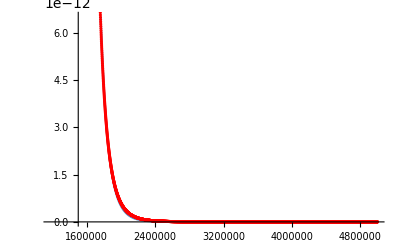

```mathematica
Show[Plot[EY92[x]-1,{x,Min[reshaped[[;;,1]]],Max[reshaped[[;;,1]]]},PlotLegends->"EY92"],ListPlot[reshaped,PlotLegends->"test model",PlotStyle->Red]]
```

Comparing Lorentz-Lorenz Variation with Parameters

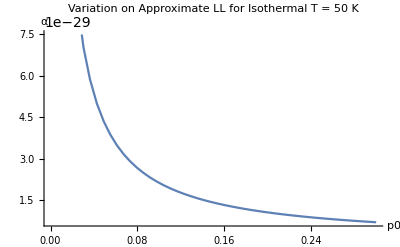

```mathematica
n0 = EY92[plutoRadius];

Plot[((R T (n0^2-1))/(4 π NAvagadro E^0))/p0x,{p0x,0.00001,0.3},AxesLabel->{"p0","α"},PlotLabel->"Variation on Approximate LL for Isothermal T = 50 K"]

Manipulate[
Plot3D[{((R Tx (n0^2-1))/(4 π NAvagadro E^0))/Pressure[p0x,μN2,r,T]*10^30,{1.171*(1-χ)+2.65*χ} (* molar fraction of Subscript[N, 2] vs Subscript[CH, 4] *)},
{p0x,0.1,1},
{Tx,20,250},
AxesLabel->{"p_0 (Pa)","T (K)","α (Å^3)"},
PlotLabel->"N_2/CH_4 mix",
ClippingStyle->None],
{r,plutoRadius,1.5*plutoRadius},
{χ,0,1}
]
```

Checking Lorentz-Lorenz Approximation Accuracy

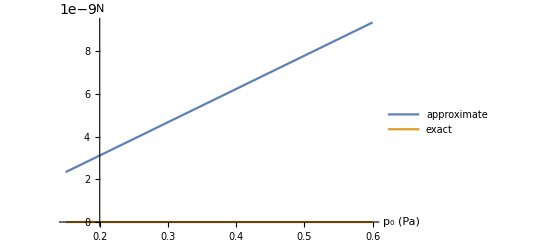

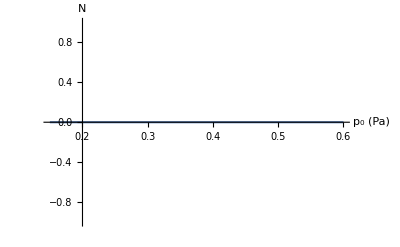

{2.5844719107630769946121326047×10^-33,5.16894382152615398922426520932×10^-33,7.75341573228923098383639781398×10^-33,1.03378876430523079784485304186×10^-32,1.29223595538153849730606630233×10^-32,1.5506831464578461967672795628×10^-32,1.80913033753415389622849282326×10^-32,2.06757752861046159568970608373×10^-32,2.3260247196867692951509193442×10^-32,2.58447191076307699461213260466×10^-32,2.84291910183938469407334586513×10^-32,3.101366292915692393534559125594×10^-32,3.35981348399200009299577238606×10^-32,3.618260675068307792456985646526×10^-32,3.876707866144615491918198906992×10^-32,4.135155057220923191379412167458×10^-32,4.393602248297230890840625427924×10^-32,4.652049439373538590301838688391×10^-32,4.910496630449846289763051948857×10^-32,5.168943821526153989224265209323×10^-32,5.427391012602461688685478469789×10^-32,5.685838203678769388146691730255×10^-32,5.944285394755077087607904990721×10^-32,6.202732585831384787069118251188×10^-32,6.461179776907692486530331511654×10^-32,6.71962696798400018599154477212×10^-32,6.978074159060307885452758032586×10^-32,7.236521350136615584913971293052×10^-32,7.494968541212923284375184553518×10^-32}

{1.556405499453953098305028530255617819720163512627093235494137564324172877225005427620689996×10^-9,3.112810996485508125420015219124747460081232818871924777642692350377102514328977488534003275×10^-9,4.669216491094665092655661035791729301168151094737954333488998835398724749082206390681729399×10^-9,6.225621983281424011322666861420718589448139119830624565573991512665102102315267089096162976×10^-9,7.782027473045784892731733489155686396736384771465543002455027391415695556234171307630723636×10^-9,9.338432960387747748193561624120420579161719085921616772381780021335419154943421035911381496×10^-9,1.0894838445307312589018851883418526736132278886839370136789066530453492996551571098390159107×10^-8,1.2451243927804479426518304796133429169301155980764674800261815985226493335457562318707781039×10^-8,1.4007649407879248272002620803328371841532032919838122973622734201587015186272665697738186815×10^-8,1.5564054885531619136782500258046419335864805331630273166788566955862013014448059136893206186×10^-8,1.712046036076159203216864342531045781448119081612299868803621036469616881017751890372732405×10^-8,1.8676865833569166969471750482123195977670324409837168826315264023455554068654125673768647763×10^-8,2.0233271303954343960002521517467166022794340617106892693238969313035402938404937095037774041×10^-8,2.1789676771917123015071656532304724603253942008500555701380822105552998047333942999078531863×10^-8,2.3346082237457504145989855439578053787453954386388878655499495920072488270396973298706768395×10^-8,2.4902487700575487364067818064209162017768868517660229433310058400282908960638250027294580937×10^-8,2.6458893161271072680616244143099885069508368433583417232414810806933759923762641731409223696×10^-8,2.8015298619544260106945833325131887009882846296818199360002427038824214672626068457236256823×10^-8,2.9571704075395049654367285171166661156968903835573730541919415517242386249124596885605628436×10^-8,3.1128109528823441334191299154045531038674840344915184727713274089960060144076235869793514044×10^-8,3.268451497982943515772857465858965135170612725521877936824205493220592357794397089879403165×10^-8,3.4240920428413031136289810981600008920530869267775432142440403243466572623769840115597905159×10^-8,3.5797325874574229281185707331857423656345252057543280109827480360499464355603532819390645982×10^-8,3.7353731318313029603726962830122549516038976543049291265337528728585500388140762311654096866×10^-8,3.8910136759629432115224276509135875461160679723440198473049182994801080833362207033101397949×10^-8,4.0466542198523436826988347313617726416883342082682985755384978308950253834808805790391638735×10^-8,4.2022947634995043750329874100268264230969681560915156914347853739767005446869313182804075618×10^-8,4.357935306904425289655955563776748863273753409294501646135679553607578770221694888870662104×10^-8,4.5135758500671064276988090606775238192025220713902192832239111784785069252439388123885400178×10^-8}

```mathematica
Plot[{LorentzLorenz[αN2,p0x,T]-1,LLExact[αN2,p0x,T]},{p0x,0.5`100*p0,2`100 p0},AxesLabel->{"p_0 (Pa)","N"},PlotLegends-> {"approximate","exact"}]
Plot[LLExact[αN2,p0x,T],{p0x,0.5*p0,2 p0},AxesLabel->{"p_0 (Pa)","N"},PlotLegends-> "exact"]

Table[LLExact[αN2,p0x,T],{p0x,0.1`100,3`100,0.1`100}]
Table[LorentzLorenz[αN2,p0x,T]-1,{p0x,0.1`100,3`100,0.1`100}]
```